```mathematica
g[n_,m_]:=(n+m-1)!/(n!(m-1)!)
g[2,6]
```

21

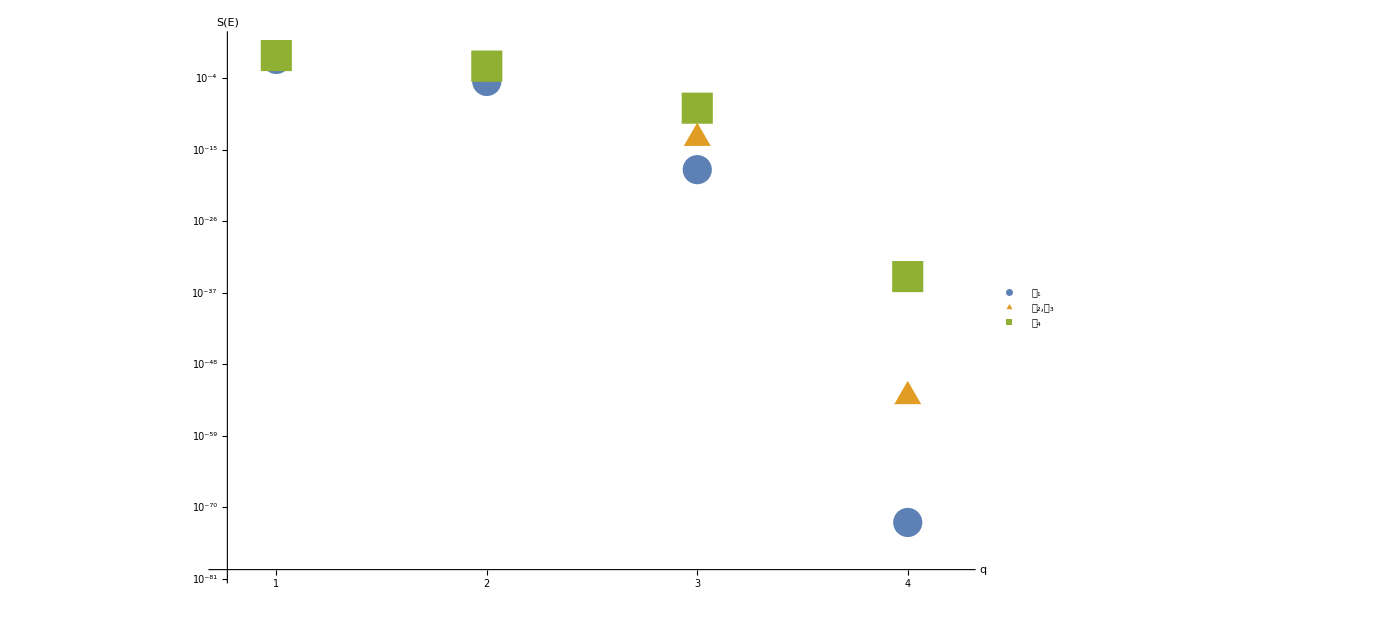

```mathematica
p1C2T[q_]:=(2/27)^(2^(2 q -2));
p2C2T[q_]:=(0.0221391)^(2^(2 q -3));
p1C4T[q_]:=(0.0221266)^(2^(2 q - 3));
p2C4T[q_]:=(0.00695043)^(2^(2 q - 4));
graphsize = 4;
C1=Table[{q,p1C2T[q]},{q,1,graphsize}];
C2=Table[{q,p2C2T[q]},{q,1,graphsize}];
C3=Table[{q,p1C4T[q]},{q,1,graphsize}];
C4=Table[{q,p2C4T[q]},{q,1,graphsize}];
ListLogPlot[{C1,C2,C4},AxesLabel->{"q","S(E)"},Ticks->{Table[i,{i,1,graphsize}],{N[2/27],N[1/10^14],N[1/10^55]}},PlotMarkers->{{●,30},{▲,32},{■,32}},LabelStyle->{FontSize-> 30},PlotLegends->Placed[PointLegend[Automatic,LegendMarkers->{{●,30},{▲,32},{■,32}},{"𝒞_1","𝒞_2,𝒞_3","𝒞_4"},LegendFunction->"Frame"],{.75,.2}],PlotRange->{{0.75,4.25},{10^-80,2/27+30}}]
```